# Time series analysis

## Auxiliary functions

### correlationPlots

```mathematica
ClearAll[correlationPlots]

Options[correlationPlots] = Flatten[{
	"Lags" -> 20
}];

correlationPlots[data_TemporalData, opts: OptionsPattern[]] :=
Module[
	{thisData},
	thisData = data["Values"];
	If[
		MatchQ[thisData, _StructuredArray],
		thisData = QuantityMagnitude[thisData] 
	];
	correlationPlots[thisData, opts]
]

correlationPlots[data: {__?NumericQ}, opts: OptionsPattern[]] :=
correlationPlots[data, Length[data], opts]

correlationPlots[model_, dataPoints_, opts: OptionsPattern[]] :=
Module[
	{
		lags, 
		data,
		linePlot, acfPlot, pacfPlot
	},
	lags = OptionValue["Lags"];
	
	data = 
	Switch[
		model,
		_?(!StringFreeQ[ToString[Head[#]], "Process"] &), RandomFunction[model, {1, dataPoints}],
		_, model
	];
	
	linePlot =
	ListLinePlot[
		data,
		Frame->True,
		PlotRange->All,
		AspectRatio->1/(2GoldenRatio),
		GridLines->Automatic,
		GridLinesStyle->Directive[{Thickness[.001],LightGray}],
		ImageSize->Scaled[1.]
	];
	
	acfPlot =
	DiscretePlot[
		CorrelationFunction[data, h], {h, 1, lags},
		Epilog -> {
			Dashed,
			Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],
			Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
		},
		PlotLabel->"ACF",
		ExtentSize->.5,
		PlotRange->{Automatic,{-1,1}},
		ImageSize->Scaled[.49]
	];
	
	pacfPlot =
	DiscretePlot[
		PartialCorrelationFunction[data,h],{h, 1, lags},
		Epilog -> {
			Dashed,
			Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],
			Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
		},
		PlotLabel->"PACF",
		ExtentSize->.5,
		PlotRange->{Automatic,{-1,1}},
		ImageSize->Scaled[.49]
	];
	
	Column[
		{
			linePlot,
			Spacer[1],
			Row[{acfPlot, pacfPlot}]
		}
	]
]
```

### summaryHistogram

```mathematica
ClearAll[summaryHistogram]

summaryHistogram[values_, binSize_] :=
Module[
	{
		mean, std, skewness, kurtosis,
		histogram, grid
	},
	{mean, std, skewness, kurtosis} = Through[{Mean, StandardDeviation, Skewness, Kurtosis}[values]];
	
	histogram = Histogram[values, binSize, "Probability", ImageSize -> Scaled[.5]];
	grid = Grid[
		{
			{Mean, StandardDeviation, Skewness, Kurtosis},
			{mean, std, skewness, kurtosis}
		},
		ItemSize -> 10,
		Frame -> All,
		FrameStyle -> Directive[{LightGray, Opacity[.5]}],
		BaseStyle -> {FontFamily -> "Helvetica"}
	];
	
	Framed[#, RoundingRadius -> 5, FrameStyle -> LightGray] & @
	Column[
		{
			histogram,
			grid
		},
		Alignment -> Center,
		Spacings -> 1.5
	]
]
```

## Electrical Load Data

```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
loadTraining =TimeSeries[TimeSeriesWindow[loadTimeSeriesResampled,{DateObject[{2012,9,28}],DateObject[{2019,6,1}]}]];
loadTest=TimeSeries[TimeSeriesWindow[loadTimeSeriesResampled,{DateObject[{2019,6,2}],DateObject[{2019,6,8}]}]];
```

### Pipeline

#### Plot the data!

```mathematica
plot=
DateListPlot[
loadTraining ,
FrameLabel->Automatic,
PlotRange->All,
AspectRatio->1/(2GoldenRatio),
GridLines->Automatic,
GridLinesStyle->Directive[{Thickness[.0001],LightGray}],
ImageSize->Large,
Mesh->All,
PlotMarkers->Graphics[{EdgeForm[{Thick,ColorData[97][1]}],White,Disk[{0,0},Scaled[.015]]}]
]
```

#### Is there a trend?

```mathematica
loadTraining ["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
values=N@TimeSeriesMap[QuantityMagnitude,loadTraining ]["Values"]
```

{11641.4,10883.1,10707.6,10663.2,10627.7,10848.8,11520.7,12877.6,14087.2,14646.6,14992.9,15267.5,15400.2,15361.9,15344.1,15176.5,15081.6,15134.4,15283.5,58474,9528.55,9547.94,10025.8,10412.2,10958.8,10999.2,10849.6,10863.,10889.4,11002.4,11263.1,11571.4,11965.6,12325.8,12536.9,12568.7,12682.3,12307.2,11450.3}
 |  |  |  |

```mathematica
linModel=LinearModelFit[values,t,t]
```

FittedModel[15022.2-0.0237626 t]

```mathematica
linModel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 15022.2 | 21.2424 | 707.179 | 0.
t | -0.0237626 | 0.000628802 | -37.7903 | 8.79571×10^-309

Estimated slope is compatible with 0.!

#### Is there a seasonal pattern?

Should we expect any seasonality?

Can we see any seasonality in the data?

```mathematica
plot
```

Look at the autocorrelation of the time series to search for the period of correlations:

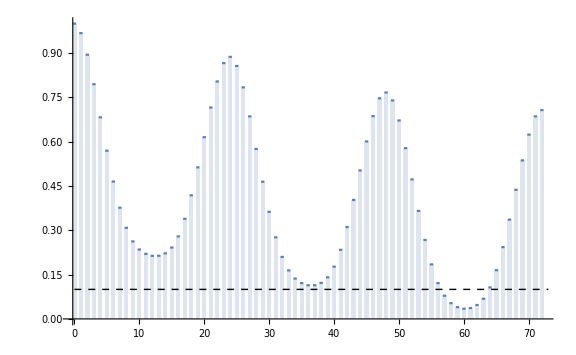

```mathematica
With[
{
data=values,
dataPoints=400,
lags=72
},
DiscretePlot[
CorrelationFunction[data,h],
{h,0,lags},
ExtentSize->.5,
PlotRange->All,
Epilog -> {
Dashed,
Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
},
ImageSize->Large
]
]
```

Let’s look at how much each hour deviates from the mean in average:

```mathematica
(* deviations from the mean *)
deviations=values-Mean[values]
```

{-2685.57,-3443.83,-3619.39,-3663.79,-3699.31,-3478.15,-2806.31,-1449.42,-239.765,58494,-3063.86,-2755.61,-2361.38,-2001.16,-1790.11,-1758.25,-1644.71,-2019.78,-2876.64}
 |  |  |  |

```mathematica
(* partition the data *)
partitionDeviations=Partition[deviations,24]
```

{{-2685.57,-3443.83,-3619.39,18,514.925,-349.525,-1488.25},2436,{1}}
 |  |  |  |

```mathematica
(* gather the contributions for each hour *)
gatherDeviationsByHour=Transpose[partitionDeviations]
```

{{-2685.57,-3081.73,-3406.06,2432,-3429.,-3480.29,-3818.83},22,{1}}
 |  |  |  |

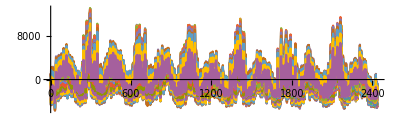

```mathematica
ListLinePlot[gatherDeviationsByHour,PlotStyle->Thick,AspectRatio->1/(2GoldenRatio),ImageSize->Scaled[.95],AxesOrigin->{1,Automatic},PlotLegends->Placed[Automatic,Bottom]]
```

```mathematica
(* mean deviation per hour *)
meanDeviationPerHour=Mean/@gatherDeviationsByHour
```

{-1191.39,-1962.39,-2332.04,-2487.46,-2545.13,-2462.47,-2125.09,-1367.91,-399.856,236.701,586.863,820.104,953.2,989.712,1023.76,1032.73,1074.33,1272.36,1711.94,2119.85,2125.,1838.4,1114.74,-25.9349}

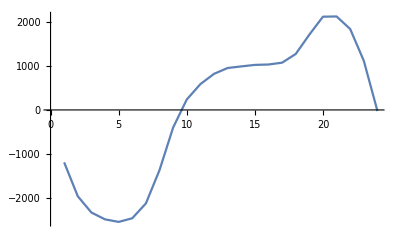

```mathematica
ListLinePlot[meanDeviationPerHour]
```

```mathematica
(* hourly deviations *)
seasonalityRules=Thread[Range[Length[meanDeviationPerHour]]->meanDeviationPerHour]
```

{1→-1191.39,2→-1962.39,3→-2332.04,4→-2487.46,5→-2545.13,6→-2462.47,7→-2125.09,8→-1367.91,9→-399.856,10→236.701,11→586.863,12→820.104,13→953.2,14→989.712,15→1023.76,16→1032.73,17→1074.33,18→1272.36,19→1711.94,20→2119.85,21→2125.,22→1838.4,23→1114.74,24→-25.9349}

```mathematica
(* seasonality series *)
seasonalitySeries=Flatten[Table[Range[24],{DateDifference[DateObject[{2012,9,28}],DateObject[{2019,6,1}]]}]]/.seasonalityRules
```

{-1191.39,-1962.39,-2332.04,58482,1838.4,1114.74,-25.9349}
 |  |  |  |

Compare the average hourly deviation from the mean with the actual time series:

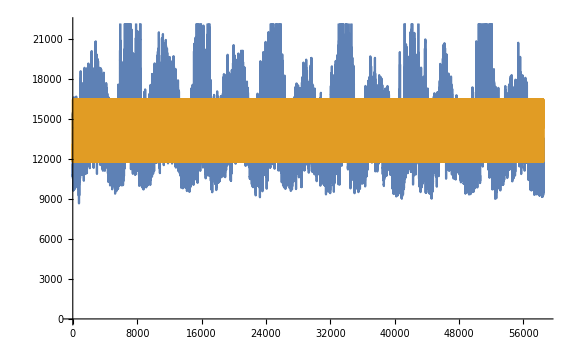

```mathematica
ListLinePlot[{values,seasonalitySeries+Mean[values]},Epilog:>{Thick,Dashed,Gray,Line[{{0,Mean[values]},{60,Mean[values]}}]},ImageSize->Large]
```

Compare the seasonally adjusted time series with the actual one:

```mathematica
residuals=values-Mean[values]-Flatten[seasonalitySeries]
```

Thread::tdlen: Objects of unequal length in «1» cannot be combined.

-14327.+11{11641.4,10883.1,10707.6,10663.2,10627.7,10848.8,58500,12325.8,12536.9,12568.7,12682.3,12307.2,11450.3}
 |  |  |  |

```mathematica
ListLinePlot[{values-Mean[values],residuals},ImageSize->Large]
```

Look at the distribution of the residuals:

```mathematica
summaryHistogram[residuals,{0.5}]
```

Do we still have any appealing pattern in the autocorrelation plot?

```mathematica
With[
{
data=residuals,
dataPoints=60,
lags=30
},
DiscretePlot[
CorrelationFunction[data,h],
{h,0,lags},
ExtentSize->.5,
PlotRange->{-1,1},
Epilog -> {
Dashed,
Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
},
ImageSize->Large
]
]
```

#### Measure of the quality of our model

How well are we fitting the training data? Compare the sum of squares of the residuals to the variance of the data:

```mathematica
Total[(values-Mean[values])^2]
```

```mathematica
Total[residuals^2]
```

```mathematica
(* coefficient of determination: R^2 -> measure how much of the variance of the data that is captured by our model *)
rSquaredTraining=1-Total[residuals^2]/Total[(values-Mean[values])^2]
```

#### Modelling the residuals

We saw above that the residuals are very well aproximated by a normal distribution with 0. mean and standard deviation 1.29, hence:

```mathematica
𝒟1=NormalDistribution[Mean[residuals],StandardDeviation[residuals]]
```

Alternatively, we could estimate a probability distribution using a SmoothKernelDistribution:

```mathematica
𝒟2=SmoothKernelDistribution[residuals]
```

Another possibility yet would be to use the function FindDistribution which would try and find a known distribution that fits well the sample data:

```mathematica
FindDistribution[residuals,10,All,RandomSeeding->1234]
```

```mathematica
𝒟3=FindDistribution[residuals,RandomSeeding->1234]
```

Comparing the PDF’s generated by these different approachs:

```mathematica
Plot[Evaluate[Table[PDF[dist][x],{dist,{𝒟1,𝒟2,𝒟3}}]],{x,-4,4},ImageSize->Large,PlotLegends->Placed[{"𝒟1","𝒟2","𝒟3"},Bottom],PlotRange->All]
```

#### Forecasting

We want the produce forecast for the period of Jan 2015 until Jun 2017, i.e. 30 months

```mathematica
forecastMean=Table[Mean[values],{30}]
```

```mathematica
forecastSeasonality=Take[Flatten[Table[Range[12],{3}]]/.seasonalityRules,30]
```

```mathematica
medianForecast=forecastMean+forecastSeasonality;
```

```mathematica
ClearAll[upperConfLimit]
upperConfLimit[dist_]:=forecastMean+forecastSeasonality+2StandardDeviation[dist]
```

```mathematica
ClearAll[lowerConfLimit]
lowerConfLimit[dist_]:=forecastMean+forecastSeasonality-2StandardDeviation[dist]
```

```mathematica
With[{dist=𝒟1},ListLinePlot[{medianForecast,upperConfLimit[dist],lowerConfLimit[dist],loadTest["Values"]},PlotStyle->{Automatic,Directive[{Dashed,LightGray}],Directive[{Dashed,LightGray}]},Filling->{2->{1},3->{1}},PlotLegends->{"Predictions","2 std band",None,"Actuals"},ImageSize->Large]]
```

#### Measure of the quality of our predictions

How well are we fitting the test data? Compare the sum of squares of the residuals to the variance of the data:

```mathematica
valuesTest=N@TimeSeriesMap[QuantityMagnitude,loadTest]["Values"];
```

```mathematica
residualsTest=medianForecast-valuesTest;
```

```mathematica
Total[(valuesTest-Mean[valuesTest])^2]
```

```mathematica
Total[residualsTest^2]
```

```mathematica
rSquaredTest=1-Total[residualsTest^2]/Total[(valuesTest-Mean[valuesTest])^2]
```

### Predicting with the built-in tools

```mathematica
tsModel=TimeSeriesModelFit[values]
```

```mathematica
tsModel["Properties"]
```

```mathematica
TimeSeriesForecast[tsModel,{30}]
```

```mathematica
DateListPlot[RandomFunction[tsModel,{29},100]]
```

```mathematica
paths=RandomFunction[tsModel,{29},10000]
```

```mathematica
Histogram[test[[1]]]
```

```mathematica
test=Sort/@Transpose[paths["ValueList"]];
```

```mathematica
tsModelMedianForecast=#[[5000]]&/@(Sort/@Transpose[paths["ValueList"]])
```

```mathematica
tsModelUpperBandForecast=#[[9770]]&/@(Sort/@Transpose[paths["ValueList"]])
```

```mathematica
tsModelLowerBandForecast=#[[230]]&/@(Sort/@Transpose[paths["ValueList"]])
```

```mathematica
(* R^2 in the training data *)
tsModelR2Training=1-Total[(tsModel["FitResiduals"]["Values"])^2]/Total[(values-Mean[values])^2]
```

```mathematica
(* R^2 in the test data *)
tsModelR2Test=1-Total[(tsModelMedianForecast-valuesTest)^2]/Total[(valuesTest-Mean[valuesTest])^2]
```

```mathematica
ListLinePlot[{tsModelMedianForecast,tsModelUpperBandForecast,tsModelLowerBandForecast,valuesTest},PlotStyle->{Automatic,Directive[{Dashed,LightGray}],Directive[{Dashed,LightGray}]},Filling->{2->{1},3->{1}},PlotLegends->{"Predictions","2 std band",None,"Actuals"},ImageSize->Large]
```